Testing Spatial Audio on a Single Plane - 2D

## Determining Delay with Dist. to Ears

Graphical Visualization

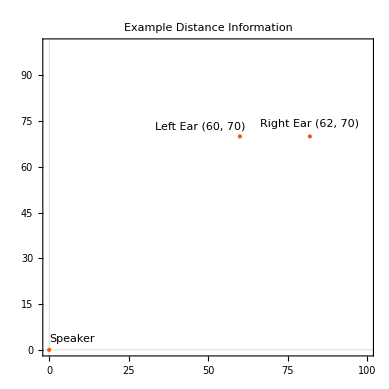

```mathematica
ListPlot[{
Labeled[{0,0},"Speaker"],
Labeled[{60,70}, "Left Ear (60, 70)"],
Labeled[{82,70}, "Right Ear (62, 70)"]
},
PlotTheme->"Scientific",
PlotRange->{{0,100},{0,100}},
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Example Distance Information"]
```

Assigning Attributes

```mathematica
distanceLeftEar = √(60^2+70^2)
distanceRightEar = √(62^2+70^2)
thetaLeftEar =1/Degree*ArcTan[70./60.] 
thetaRightEar = 1/Degree*ArcTan[70./62.]
```

10 √85

2 √2186

49.3987

48.4682

```mathematica
Quantity[8,"m/s"]
```

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[8,m/s]]

## Working with Audio Functions to Channel Delay

## GUI Implementation